```mathematica
(* MKM 505E - Advanced Control Methods in Mechatronics - Midterm Exam *)
```

```mathematica
(* Mertcan Kaya (518192004) *)
```

```mathematica
(* Question 1 *)
```

```mathematica
(* i) Build the system matrix *)
```

```mathematica
(* State-Space Description *)
```

```mathematica
Amat = {{-0.275,2.682,-0.0067,0},{-0.994,-0.125,-0.003,0.074},{0.365,-6.695,-1.004,0},{-0.002,0,1,0}};
```

```mathematica
Bmat={{0.094,-2.169},{0,0.038},{0.611,1.190},{0,0}};
```

```mathematica
Cmat={{0,1,0,0},{0,0,0,1}};
```

```mathematica
Dmat={{0,0},{0,0}};
```

```mathematica
sI={{s,0,0,0},{0,s,0,0},{0,0,s,0},{0,0,0,s}};
```

```mathematica
SysMat = {{sI-Amat,Bmat},{-Cmat,Dmat}};
```

```mathematica
(* System Matrix *)
```

```mathematica
MatrixForm[ArrayFlatten[SysMat]]
```

(0.275+s | -2.682 | 0.0067 | 0 | 0.094 | -2.169
0.994 | 0.125+s | 0.003 | -0.074 | 0 | 0.038
-0.365 | 6.695 | 1.004+s | 0 | 0.611 | 1.19
0.002 | 0 | -1 | s | 0 | 0
0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0)

```mathematica
(* ii) Find the transfer function of the system *)
```

```mathematica
Tmat=sI-Amat;
```

```mathematica
Umat = Bmat;
```

```mathematica
Vmat=Cmat;
```

```mathematica
Wmat=Dmat;
```

```mathematica
(* Transfer Function *)
```

```mathematica
Gmat=Simplify[Vmat.Inverse[Tmat].Umat+Wmat];
```

```mathematica
MatrixForm[Gmat]
```

((0.0149594-0.0451475 s-0.095269 s^2)/(0.0642076+3.24922 s+3.08424 s^2+1.404 s^3+s^4) | (-0.0340447+2.27289 s+2.20102 s^2+0.038 s^3)/(0.0642076+3.24922 s+3.08424 s^2+1.404 s^3+s^4)
(2.27971+0.278506 s+0.610812 s^2)/(0.0642076+3.24922 s+3.08424 s^2+1.404 s^3+s^4) | (-11.3524-0.565385 s+1.19434 s^2)/(0.0642076+3.24922 s+3.08424 s^2+1.404 s^3+s^4))

```mathematica
(* iii) Find the invariant zeros of the system *)
```

```mathematica
GmatDenom=Denominator[Gmat];
```

```mathematica
(*d=PolynomialLCM[GmatDenom[[1,1]],GmatDenom[[1,2]],GmatDenom[[2,1]],GmatDenom[[2,2]]]*)
```

```mathematica
d=GmatDenom[[1,1]]
```

0.0642076+3.24922 s+3.08424 s^2+1.404 s^3+s^4

```mathematica
Nmat=Gmat d;
```

```mathematica
MatrixForm[Nmat]
```

(0.0149594-0.0451475 s-0.095269 s^2 | -0.0340447+2.27289 s+2.20102 s^2+0.038 s^3
2.27971+0.278506 s+0.610812 s^2 | -11.3524-0.565385 s+1.19434 s^2)

```mathematica
(* Smith Form *)
```

```mathematica
eps0=1;
```

```mathematica
eps1=PolynomialGCD[Nmat[[1,1]],Nmat[[1,2]],Nmat[[2,1]],Nmat[[2,2]]]
```

1.

```mathematica
eps2=-Simplify[Det[Nmat]]
```

0.0922141+4.66797 s+4.50497 s^2+2.08799 s^3+1.46877 s^4+0.0232109 s^5

```mathematica
phi1=eps1/eps0
```

1.

```mathematica
phi2=Simplify[eps2/eps1]
```

0.0922141+4.66797 s+4.50497 s^2+2.08799 s^3+1.46877 s^4+0.0232109 s^5

```mathematica
Smat={{phi1,0},{0,phi2}};
```

```mathematica
MatrixForm[Smat]
```

(1. | 0
0 | 0.0922141+4.66797 s+4.50497 s^2+2.08799 s^3+1.46877 s^4+0.0232109 s^5)

```mathematica
(* McMillian Form *)
```

```mathematica
Mmat=FullSimplify[Smat/d];
```

```mathematica
MatrixForm[Mmat]
```

(1./(0.0642076+s (3.24922+s (3.08424+s (1.404+s)))) | 0
0 | (4.57807+s (4.4635+s (2.05842+(1.46831+0.0232109 s) s)))/(3.18765+s (3.05637+s (1.38386+1. s))))

```mathematica
(* Invariant Zeros:  *)
```

```mathematica
InvarZeros=s/.Solve[Smat[[2,2]]==0,s]
```

{-61.8756,-1.14533,-0.119264-1.66402 ⅈ,-0.119264+1.66402 ⅈ,-0.0201426}

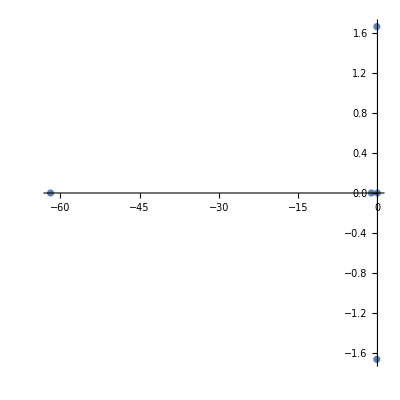

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@InvarZeros,AspectRatio->1]
```

```mathematica
(* iv) Find the transmission zeros of the system *)
```

```mathematica
(* Transmission Zeros: all zeros lie in the open left half of the complex-plane *)
```

```mathematica
TransZero=s/.Solve[Numerator[Mmat[[2,2]]]==0,s]
```

{-61.8756,-1.14533,-0.119264-1.66402 ⅈ,-0.119264+1.66402 ⅈ}

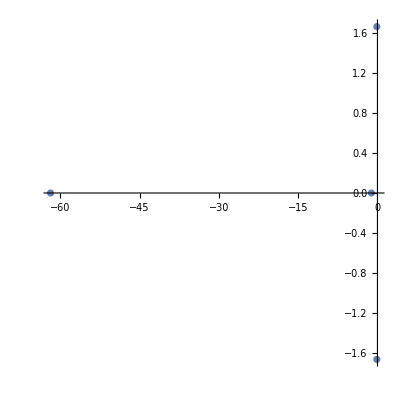

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@TransZero,AspectRatio->1]
```

```mathematica
(* v) Find the controllability matrix *)
```

```mathematica
(* det(Gmat)≠0, so a necessary condition is satisfied *)
```

```mathematica
DetGmat=Simplify[Det[Gmat]]
```

(-0.0922141-4.66797 s-4.50497 s^2-2.08799 s^3-1.46877 s^4-0.0232109 s^5)/((0.0642076+3.24922 s+3.08424 s^2+1.404 s^3+s^4)^2)

```mathematica
(* P=[B|AB|A^2B|A^3B] *)
```

```mathematica
Pmat={{Bmat,Amat.Bmat,MatrixPower[Amat,2].Bmat,MatrixPower[Amat,3].Bmat}};
```

```mathematica
MatrixForm[Pmat]
```

((0.094 | -2.169
0 | 0.038
0.611 | 1.19
0 | 0) | (-0.0299437 | 0.690418
-0.095269 | 2.14767
-0.579134 | -2.24086
0.610812 | 1.19434) | (-0.243397 | 5.58519
0.0886102 | -0.85963
1.20835 | -11.8768
-0.579074 | -2.24224) | (0.296491 | -3.76188
0.184384 | -5.57452
-1.89527 | 19.7181
1.20883 | -11.888))

```mathematica
(*rank(P)=4=n (The system is controllable, n: order of the system) *)
```

```mathematica
MatrixRank[ArrayFlatten[Pmat]]
```

4

```mathematica
(* vi) Find the observability matrix *)
```

```mathematica
Qmat={{Cmat},{Cmat.Amat},{Cmat.MatrixPower[Amat,2]},{Cmat.MatrixPower[Amat,3]}};
```

```mathematica
MatrixForm[Qmat]
```

((0 | 1 | 0 | 0
0 | 0 | 0 | 1)
(-0.994 | -0.125 | -0.003 | 0.074
-0.002 | 0. | 1. | 0.)
(0.396357 | -2.6302 | 0.0840468 | -0.00925
0.36555 | -6.70036 | -1.00399 | 0.)
(2.53611 | 0.829111 | -0.088398 | -0.194635
6.19318 | 8.53964 | 1.02565 | -0.495827))

```mathematica
(* rank(Q)=4=n (The system is observable, n: order of the system) *)
```

```mathematica
MatrixRank[ArrayFlatten[Qmat]]
```

4

```mathematica
(* vii) Is the system output controllable? *)
```

```mathematica
PoMat={{Cmat.Bmat,Cmat.Amat.Bmat,Cmat.MatrixPower[Amat,2].Bmat,Cmat.MatrixPower[Amat,3].Bmat,Dmat}};
```

```mathematica
MatrixForm[PoMat]
```

((0. | 0.038
0. | 0.) | (-0.095269 | 2.14767
0.610812 | 1.19434) | (0.0886102 | -0.85963
-0.579074 | -2.24224) | (0.184384 | -5.57452
1.20883 | -11.888) | (0 | 0
0 | 0))

```mathematica
(* rank(Po)=2=m (The system is output controllable, m: number of the outputs) *)
```

```mathematica
MatrixRank[ArrayFlatten[PoMat]]
```

2

```mathematica
(* viii) Find the eigenvalues of A. Is the system stable? *)
```

```mathematica
(* a) Use direct function *)
```

```mathematica
Eigenvalues[Amat]
```

{-0.119264+1.66402 ⅈ,-0.119264-1.66402 ⅈ,-1.14533+0. ⅈ,-0.0201426+0. ⅈ}

```mathematica
(* b) Find roots of det(sI-A) *)
```

```mathematica
MatrixForm[sI-Amat]
```

(0.275+s | -2.682 | 0.0067 | 0
0.994 | 0.125+s | 0.003 | -0.074
-0.365 | 6.695 | 1.004+s | 0
0.002 | 0 | -1 | s)

```mathematica
Det[sI-Amat]
```

0.0642076+3.24922 s+3.08424 s^2+1.404 s^3+s^4

```mathematica
eigAmat=s/.Solve[Det[sI-Amat]==0,s]
```

{-1.14533,-0.119264-1.66402 ⅈ,-0.119264+1.66402 ⅈ,-0.0201426}

```mathematica
(* Both a) and b) gives exactly same results *)
```

```mathematica
(* Eigenvalues of A lie in the left hald of the complex-plane, hence the system is stable *)
```

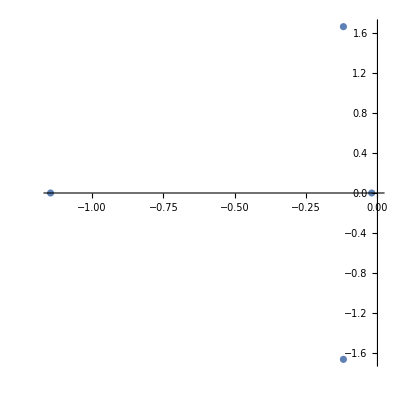

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@eigAmat,AspectRatio->1]
```

```mathematica
(* ix) Design a static state feedback controller to assign the poles at {-1.4,-0.15-1.8i,-0.15+1.8i,-0.035} *)
```

```mathematica
(* First four columns of controllability matrix are linearly independent and used for generating M matrix *)
```

```mathematica
Mmat=Transpose[{Bmat[[All,1]],Amat.Bmat[[All,1]],Bmat[[All,2]],Amat.Bmat[[All,2]]}];
```

```mathematica
MatrixForm[Mmat]
```

(0.094 | -0.0299437 | -2.169 | 0.690418
0 | -0.095269 | 0.038 | 2.14767
0.611 | -0.579134 | 1.19 | -2.24086
0 | 0.610812 | 0 | 1.19434)

```mathematica
MmatInv=Inverse[Mmat];
```

```mathematica
MatrixForm[MmatInv]
```

(0.835287 | 0.448221 | 1.50816 | 1.5408
-0.0134495 | -0.832478 | 0.00206915 | 1.50862
-0.422467 | 0.166438 | 0.064995 | 0.0668732
0.00687837 | 0.425749 | -0.00105821 | 0.0657383)

```mathematica
Tmat=ArrayReshape[Flatten[{{MmatInv[[2]]},{MmatInv[[2]].Amat},{MmatInv[[4]]},{MmatInv[[4]].Amat}}],{4,4}];
```

```mathematica
MatrixForm[Tmat]
```

(-0.0134495 | -0.832478 | 0.00206915 | 1.50862
0.82892 | 0.0541354 | 1.50914 | -0.0616034
0.00687837 | 0.425749 | -0.00105821 | 0.0657383
-0.425603 | -0.0276861 | 0.0654775 | 0.0315054)

```mathematica
AmatBar=Chop[Tmat.Amat.Inverse[Tmat],10^-15];
```

```mathematica
MatrixForm[AmatBar]
```

(0 | 1. | 0 | 0
0.76655 | -0.941598 | -17.087 | -2.76676
0 | 0 | 0 | 1.
0.157387 | -0.00329458 | -3.42451 | -0.462402)

```mathematica
BmatBar=Chop[Tmat.Bmat,10^-15];
```

```mathematica
MatrixForm[BmatBar]
```

(0 | 0
1. | 0
0 | 0
0 | 1.)

```mathematica
CmatBar=Chop[Cmat.Inverse[Tmat],10^-15];
```

```mathematica
MatrixForm[CmatBar]
```

(-0.0951438 | 0 | 2.16524 | 0.038
0.610812 | 0 | 1.19434 | 0)

```mathematica
KmatBar={{kbar11,kbar12,kbar13,kbar14},{kbar21,kbar22,kbar23,kbar24}};
```

```mathematica
MatrixForm[KmatBar]
```

(kbar11 | kbar12 | kbar13 | kbar14
kbar21 | kbar22 | kbar23 | kbar24)

```mathematica
ABK=AmatBar+BmatBar.KmatBar;
```

```mathematica
MatrixForm[ABK]
```

(0 | 1. | 0 | 0
0.76655+1. kbar11 | -0.941598+1. kbar12 | -17.087+1. kbar13 | -2.76676+1. kbar14
0 | 0 | 0 | 1.
0.157387+1. kbar21 | -0.00329458+1. kbar22 | -3.42451+1. kbar23 | -0.462402+1. kbar24)

```mathematica
(* First Method *)
```

```mathematica
Expand[(s+1.4)(s+0.035)]
```

0.049+1.435 s+s^2

```mathematica
alphaVec1=CoefficientList[Expand[(s+1.4)(s+0.035)],s]
```

{0.049,1.435,1}

```mathematica
Chop[Expand[(s+0.15+1.8I)(s+0.15-1.8I)],10^-15]
```

3.2625+0.3 s+s^2

```mathematica
betaVec1=CoefficientList[Chop[Expand[(s+0.15+1.8I)(s+0.15-1.8I)],10^-15],s]
```

{3.2625,0.3,1}

```mathematica
(* Controllable canonical form 1 *)
```

```mathematica
CCF1={{0,1,0,0},{-alphaVec1[[1]],-alphaVec1[[2]],0,0},{0,0,0,1},{0,0,-betaVec1[[1]],-betaVec1[[2]]}};
```

```mathematica
MatrixForm[CCF1]
```

(0 | 1 | 0 | 0
-0.049 | -1.435 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -3.2625 | -0.3)

```mathematica
KmatBarN1=ArrayReshape[Flatten[{{kbar11/.Solve[ABK[[2,1]]==CCF1[[2,1]],kbar11],kbar12/.Solve[ABK[[2,2]]==CCF1[[2,2]],kbar12],kbar13/.Solve[ABK[[2,3]]==CCF1[[2,3]],kbar13],kbar14/.Solve[ABK[[2,4]]==CCF1[[2,4]],kbar14]},{kbar21/.Solve[ABK[[4,1]]==CCF1[[4,1]],kbar21],kbar22/.Solve[ABK[[4,2]]==CCF1[[4,2]],kbar22],kbar23/.Solve[ABK[[4,3]]==CCF1[[4,3]],kbar23],kbar24/.Solve[ABK[[4,4]]==CCF1[[4,4]],kbar24]}}],{2,4}];
```

```mathematica
MatrixForm[KmatBarN1]
```

(-0.81555 | -0.493402 | 17.087 | 2.76676
-0.157387 | 0.00329458 | 0.162012 | 0.162402)

```mathematica
CondNum1=First@#/Last@#&@SingularValueList[PseudoInverse[KmatBarN1]]
```

86.4874

```mathematica
(* Second Method *)
```

```mathematica
Chop[Expand[(s+1.4)(s+0.15+1.8I)(s+0.15-1.8I)(s+0.035)],10^-15]
```

0.159863+4.69639 s+3.742 s^2+1.735 s^3+s^4

```mathematica
alphaVec=CoefficientList[Chop[Expand[(s+1.4)(s+0.15+1.8I)(s+0.15-1.8I)(s+0.035)],10^-15],s]
```

{0.159863,4.69639,3.742,1.735,1}

```mathematica
(* Controllable canonical form 2 *)
```

```mathematica
CCF2={{0,1,0,0},{0,0,1,0},{0,0,0,1},{-alphaVec[[1]],-alphaVec[[2]],-alphaVec[[3]],-alphaVec[[4]]}};
```

```mathematica
MatrixForm[CCF2]
```

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
-0.159863 | -4.69639 | -3.742 | -1.735)

```mathematica
KmatBarN2=ArrayReshape[Flatten[{{kbar11/.Solve[ABK[[2,1]]==CCF2[[2,1]],kbar11],kbar12/.Solve[ABK[[2,2]]==CCF2[[2,2]],kbar12],kbar13/.Solve[ABK[[2,3]]==CCF2[[2,3]],kbar13],kbar14/.Solve[ABK[[2,4]]==CCF2[[2,4]],kbar14]},{kbar21/.Solve[ABK[[4,1]]==CCF2[[4,1]],kbar21],kbar22/.Solve[ABK[[4,2]]==CCF2[[4,2]],kbar22],kbar23/.Solve[ABK[[4,3]]==CCF2[[4,3]],kbar23],kbar24/.Solve[ABK[[4,4]]==CCF2[[4,4]],kbar24]}}],{2,4}];
```

```mathematica
MatrixForm[KmatBarN2]
```

(-0.76655 | 0.941598 | 18.087 | 2.76676
-0.31725 | -4.69309 | -0.317488 | -1.2726)

```mathematica
CondNum2=First@#/Last@#&@SingularValueList[PseudoInverse[KmatBarN2]]
```

3.80474

```mathematica
(* CondNum2 < CondNum1, hence solution of second method is beter conditioned *)
```

```mathematica
Kmat=KmatBarN2.Tmat;
```

```mathematica
MatrixForm[Kmat]
```

(-0.262316 | 8.31301 | 1.58143 | 0.0617323
-3.34649 | -0.0898956 | -7.16616 | -0.250465)